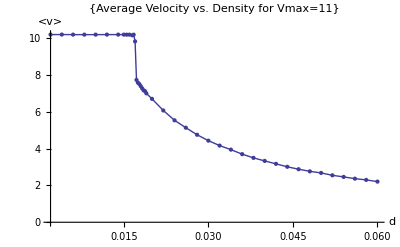

```mathematica
vbar11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax11.txt",{Number,Number}];
a=ListPlot[vbar11,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
b=ListLinePlot[vbar11,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a,b]
```

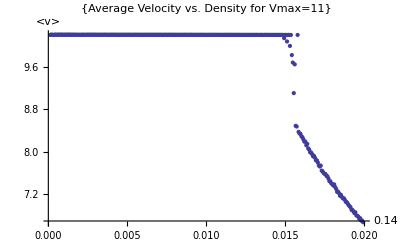

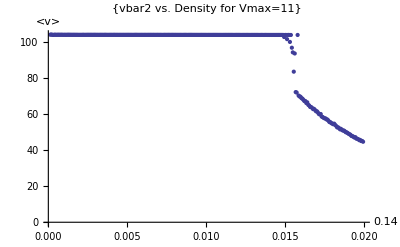

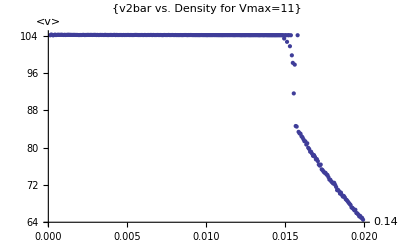

```mathematica
vbar=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar.vmax11.fine4.txt",{Number,Number}];
vbar2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar2.vmax11.fine4.txt",{Number,Number}];
v2bar=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/v2bar.vmax11.fine4.txt",{Number,Number}];
vbarf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar.vmax11.fine5.txt",{Number,Number}];
vbar2f=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar2.vmax11.fine5.txt",{Number,Number}];
v2barf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/v2bar.vmax11.fine5.txt",{Number,Number}];
a2=ListPlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
b2=ListLinePlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a2]
ListPlot[vbar2,PlotLabel->{"vbar2 vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full]
ListPlot[v2bar,PlotLabel->{"v2bar vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full]
```

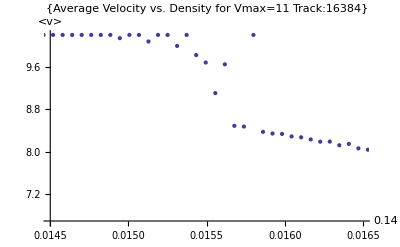

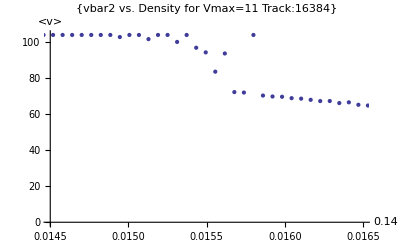

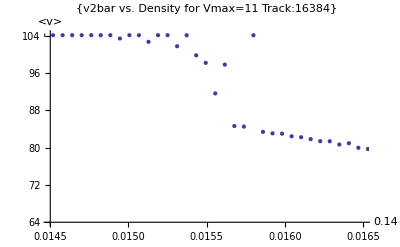

```mathematica
ListPlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=11  Track:16384"},AxesLabel->{d,"<v>"},PlotRange->{{0.0145,0.0165},Full}]
ListPlot[vbar2,PlotLabel->{"vbar2 vs. Density for Vmax=11  Track:16384"},AxesLabel->{d,"<v>"},PlotRange->{{0.0145,0.0165},Full}]
ListPlot[v2bar,PlotLabel->{"v2bar vs. Density for Vmax=11  Track:16384"},AxesLabel->{d,"<v>"},PlotRange->{{0.0145,0.0165},Full}]
```

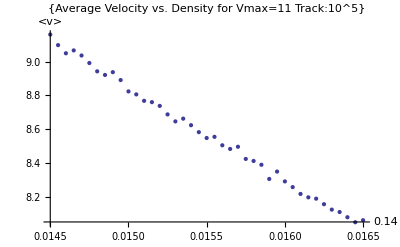

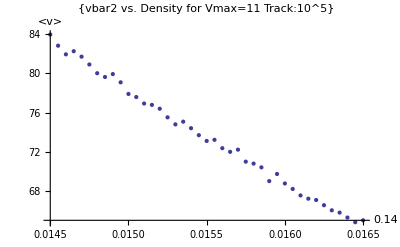

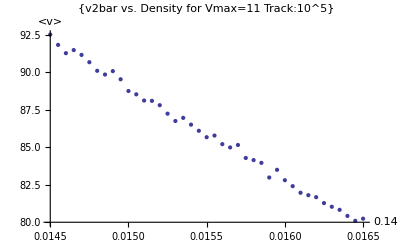

```mathematica
ListPlot[vbarf,PlotLabel->{"Average Velocity vs. Density for Vmax=11  Track:10^5"},AxesLabel->{d,"<v>"},PlotRange->Full]
ListPlot[vbar2f,PlotLabel->{"vbar2 vs. Density for Vmax=11  Track:10^5"},AxesLabel->{d,"<v>"},PlotRange->Full]
ListPlot[v2barf,PlotLabel->{"v2bar vs. Density for Vmax=11  Track:10^5"},AxesLabel->{d,"<v>"},PlotRange->Full]
```

16384. = L

8 = N

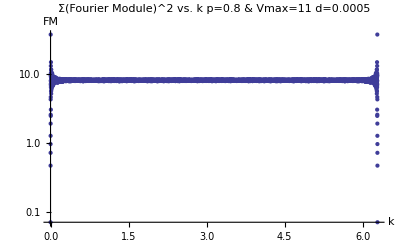

7.99658 = N*(L-N)/(L-1)

8.05777 = Mean of o.7 largest values

131008. = Sum of All L-1 Valus

131008. = N*(L-N)

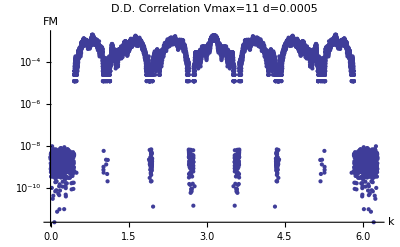

0.000427272 = (N-1)/(L-1)

0.000474705 = Mean of o.9 largest values

7. = Sum of All L Valus

7 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,3.04108×10^-9}

{1,-1.35756×10^-9}

{2,-1.28887×10^-9}

{3,2.41669×10^-9}

{4,-8.85931×10^-10}

{5,-1.40926×10^-9}

{6,-5.11413×10^-9}

{7,-2.26599×10^-9}

{8,8.24401×10^-10}

{9,1.51195×10^-9}

{10,-2.51316×10^-9}

{11,2.95622×10^-9}

{12,-2.10984×10^-9}

{13,2.70524×10^-9}

{14,-4.5917×10^-10}

{15,4.11797×10^-9}

{16,-8.66047×10^-10}

{17,2.87553×10^-9}

{18,-7.17016×10^-10}

{19,5.69275×10^-10}

{20,-2.60585×10^-9}

{21,-1.87128×10^-9}

{22,-1.05988×10^-9}

{23,-5.7086×10^-10}

{24,3.44382×10^-9}

{25,7.8735×10^-10}

{26,4.64608×10^-9}

{27,8.29352×10^-10}

{28,3.51824×10^-10}

{29,-7.28673×10^-10}

{30,6.87852×10^-10}

{31,-4.37845×10^-9}

{32,-7.43254×10^-9}

{33,-3.68584×10^-9}

{34,3.21223×10^-9}

{35,-5.41141×10^-9}

{36,1.18864×10^-9}

{37,-2.97387×10^-11}

{38,1.0641×10^-9}

{39,-1.32336×10^-9}

{40,-1.96587×10^-9}

{41,6.3946×10^-10}

{42,-2.03312×10^-9}

{43,6.89096×10^-10}

{44,1.17737×10^-9}

{45,3.15751×10^-9}

{46,3.30429×10^-9}

{47,3.21804×10^-9}

{48,4.63458×10^-9}

```mathematica
d="0.0005";
n=16384.000;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vvmax11/fourier.1d.averaged.d";
b=".p0.8.v11.txt";
g=".p0.8.v11.txt";
c=a<>d<>b;
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vvmax11/ddensitycorrelation.d";
f=e<>d<>g;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
bitf2=bitF[[All,2]];
ListLogPlot[bitF,PlotLabel->"Σ(Fourier Module)^2 vs. k  p=0.8 & Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
ListLogPlot[density,PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
p=(m-1)/(n-1);
p  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
For[i=0,i<50,i++,
If[density2[[i]]<2*p/3,
Print[{i-1,density2[[i]]}]
]
]
```

m =

262

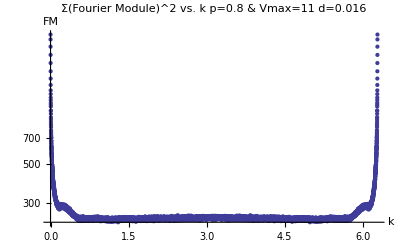

(m-1)/(N-1) * m =

4.17396

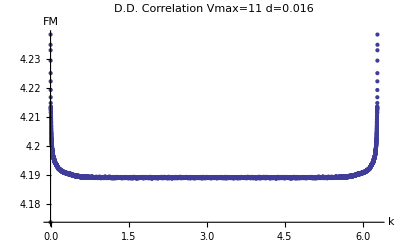

```mathematica
d="0.016";
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fourier.1d.averaged.d";
b=".p0.8.u.check.v11.txt";
c=a<>d<>b;
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/ddensitycorrelation.d";
f=e<>d<>b;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
"m ="
m
bitF=ReadList[c,{Number,Number}];
ListLogPlot[bitF,PlotLabel->"Σ(Fourier Module)^2 vs. k  p=0.8 & Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
density=ReadList[f,{Number,Number}];
"(m-1)/(N-1) * m =" 
p=(m-1)*m/16383.0;
p
ListLogPlot[density,PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
```

```mathematica
vbar11
```

{{0.002,10.199},{0.004,10.2016},{0.006,10.1978},{0.008,10.196},{0.01,10.197},{0.012,10.1995},{0.014,10.1989},{0.015,10.1974},{0.0155,10.1947},{0.016,10.1954},{0.0165,10.1585},{0.01675,10.1946},{0.017,9.8294},{0.01725,7.73553},{0.0175,7.58583},{0.01775,7.51328},{0.018,7.39788},{0.01825,7.28},{0.0185,7.17511},{0.01875,7.12855},{0.019,7.0063},{0.02,6.70615},{0.022,6.0762},{0.024,5.54008},{0.026,5.13889},{0.028,4.75471},{0.03,4.43469},{0.032,4.16637},{0.034,3.94608},{0.036,3.70047},{0.038,3.49954},{0.04,3.33292},{0.042,3.1743},{0.044,3.01473},{0.046,2.88269},{0.048,2.76728},{0.05,2.68094},{0.052,2.55126},{0.054,2.46476},{0.056,2.36879},{0.058,2.30186},{0.06,2.20854}}

```mathematica
vbar112
```

{{0.0165,10.021},{0.01675,10.1166},{0.017,8.98477},{0.01725,7.70806},{0.0175,7.6077},{0.01775,7.499},{0.018,7.386},{0.01825,7.28585},{0.0185,7.21444},{0.01875,7.10464}}